```mathematica
Quit[]
```

```mathematica
NotebookDirectory[]
```

/home/riccardo/Documents/Fisica/Tesi/Processes/diagrams/pmm2L/

## Input

```mathematica
<<"/home/riccardo/Programs/FeynArts/FeynArts/FeynArts.m";
<<"/home/riccardo/Programs/FormCalc/FormCalc/FormCalc.m";
Remove[q1];
Remove[q2];
<<"/home/riccardo/Programs/ABISS/ABISS/ABISS.m";
```

FeynArts 3.11 (25 Mar 2022)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

FormCalc 9.10 (30 Aug 2022)

by Thomas Hahn

+++++ ABISS` +++++
Version 1.0.0

Amplitudes Builder, Interference Solver and Simplifier

```mathematica
SetPath[NotebookDirectory[]];
process={F[3,{1,o}],-F[3,{1,o}]}->{F[2,{2}],-F[2,{2}]};
SetProcess[process];
```

```mathematica
GenerateInput[];
```

ABISS Warning: Input file /home/riccardo/Documents/Fisica/Tesi/Processes/diagrams/pmm2L/input/kinematics.m already exist. It will NOT be overwritten.

ABISS Warning: Input file /home/riccardo/Documents/Fisica/Tesi/Processes/diagrams/pmm2L/input/integral_families.m already exist. It will NOT be overwritten.

```mathematica
ImportInput[];
```

ABISS: Imported input file /home/riccardo/Documents/Fisica/Tesi/Processes/diagrams/pmm2L/input/kinematics.m.

ABISS: Imported input file /home/riccardo/Documents/Fisica/Tesi/Processes/diagrams/pmm2L/input/integral_families.m.

ABISS: Imported input file /home/riccardo/Documents/Fisica/Tesi/Processes/diagrams/pmm2L/input/equivalence_classes.m

## Functions

```mathematica
countInsertions[ins_]:=Module[{result,index},
result=0;
Do[
Do[
result+=Length[ins[[i,2,j,2]]];
,{j,Length[ins[[i,2]]]}];
,{i,Length[ins]}];
Return[result]
]
```

```mathematica
extractTopology[ins_Rule]:=ins[[1]];
extractLoopFields[top_]:=Module[{result},
result=Cases[top,Propagator[Loop[_]][Vertex[a1_][n1_],Vertex[a2_][n2_],f_]:>Rule[{n1,n2},f],Infinity]
]
extractLoopVertices[lines_]:=Module[{result},
result=Cases[lines,Rule[{n1_,n2_},f_]:>{n1,n2},Infinity]
]
next[{a_,b_},c_]:=Module[{result},
If[a=!=c && b=!=c,
result=c,
If[a===c,
result=b,
result=a
]
];
Return[result]
]
sortLoopFields[lines_List]:=Module[{result},
result=SortBy[lines,#[[2,1]]&]
]
```

```mathematica
triangles[top_]:=Module[{result,lines,vertices,a,b,c,verticesTmp,f1,f2,f3},
result={};
lines=extractLoopFields[top];
vertices=Map[Sort,extractLoopVertices[lines]];
Do[
a=vertices[[i,1]];
b=vertices[[i,2]];
verticesTmp=Delete[vertices,i];
Do[
If[!FreeQ[verticesTmp[[j]],a],
c=next[verticesTmp[[j]],a];
If[(!FreeQ[verticesTmp,Sort[{b,c}]]),
f1=Sort[{a,b}]/.lines;
f2=Sort[{a,c}]/.lines;
f3=Sort[{b,c}]/.lines;
result=AppendTo[result,sortLoopFields[{{Sort[{a,b}],f1},{Sort[{a,c}],f2},{Sort[{b,c}],f3}}]]
]
]
,{j,Length[verticesTmp]}]
,{i,Length[vertices]}];
Return[DeleteDuplicates[result]]
]

fermion[field_]:=Module[{result},
result=field;
If[MatchQ[field,-F[__]],
result=-field
];
Return[result]
]

deleteFermionTriangles[insertion_]:=Module[{result,n,diag,tri,rules,fields,check,deletelist},
n=countInsertions[insertion];
deletelist={};
Do[
diag=DiagramExtract[insertion,i];
tri=triangles[diag[[1,1]]];
rules=List@@diag[[1,2,1,2,1]];
If[tri=!={},
Do[
fields=DeleteDuplicates[Map[fermion[#[[2]]]&,tri[[j]]/.rules]];
If[MatchQ[fields,{F[__]}]||MatchQ[fields,{-F[__]}],
deletelist=AppendTo[deletelist,i]
]
,{j,Length[tri]}]
]
,{i,n}];
deletelist=DeleteDuplicates[deletelist];
result=DiagramDelete[insertion,deletelist];
Return[result]
]
```

```mathematica
fieldsBorn=<<(NotebookDirectory[]<>"backup/fields/fieldsBorn.m");
fields1L=<<(NotebookDirectory[]<>"backup/fields/fields1L.m");
fields2L=<<(NotebookDirectory[]<>"backup/fields/fields2L.m");
qedCondition=
(FreeQ[#,F[1,n___]]&&
FreeQ[#,V[2]]&&
FreeQ[#,V[3]]&&
FreeQ[#,S[n_]]&&
FreeQ[#,SV[n_]]&&
FreeQ[#,U[2]]&&
FreeQ[#,U[3]]&&
FreeQ[#,U[4]]&&
FreeQ[#,V[20]]&&
FreeQ[#,V[30]])&;
fieldsBornQED=DiagramSelect[fieldsBorn,qedCondition];
fields1LQED=DiagramSelect[fields1L,qedCondition];
fields2LQED=DiagramSelect[fields2L,qedCondition];
fieldsBornQEDnoT=deleteFermionTriangles[fieldsBornQED];
fields1LQEDnoT=deleteFermionTriangles[fields1LQED];
fields2LQEDnoT=deleteFermionTriangles[fields2LQED];
```

## Integral Families - Kira Reduction

In questa sezione c' è un' elenco delle integral familiy per il conto 2 Loop della correzione al vertice muonico. Ci sono 5 integral family, di ciscuno è riportata la definizione, i settori attivi degli integrali scalari e un diagramma di qualla famiglia. Di ciascuna è riportato il tempo necessario per la riduzione con kira

## A1

```mathematica
userPropagatorMomenta[A1]//MatrixForm
```

(q1
q2
q1+q2
p3+q2
-p3+q1
-p1-p2+p3+q2
p1-q1
p1-q2
p1+p2-q1)

```mathematica
userIntegralMasses[A1]
```

{M1,0,M1,M1,0,M1,0,0,0}

Settori Attivi

```mathematica
{1,1,1,1,1,1,0,0,0}
```

loading generic model file /home/riccardo/Programs/FeynArts/FeynArts/Models/Lorentzbgf.gen

> $GenericMixing is OFF

generic model {Lorentzbgf} initialized

loading classes model file /home/riccardo/Programs/FeynArts/FeynArts/Models/SMbgf_Anglerfish.mod

> 60 particles (incl. antiparticles) in 24 classes

> $CounterTerms are ON

> 689 vertices

> 334 counterterms of order 1

> 2 counterterms of order 2

classes model {SMbgf_Anglerfish} initialized

> Top. 1 aebe/cfdg/eh1f1g212f2hgh.m, 0 diagrams

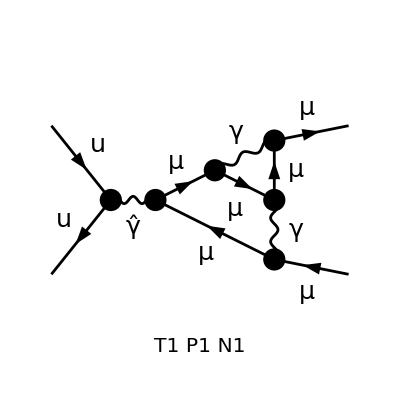

```mathematica
Paint[DiagramExtract[fields2LQEDnoT,1],ColumnsXRows->1];
```

### Tempo di riduzione con kira

```mathematica
tA1=199632.0;
Print["Ore:  ", %/3600]
```

Ore:  55.4533

## A2

```mathematica
userPropagatorMomenta[A2]//MatrixForm
```

(q1
q2
q1+q2
p3+q2
-p3+q1
-p1-p2+p3+q2
p1-q1
p1-q2
p1+p2-q1)

```mathematica
userIntegralMasses[A2]
```

{M1,0,M2,M2,0,0,0,0,M1}

Settori Attivi

```mathematica
{1,0,1,1,1,0,0,0,1}
```

> Top. 1 aebe/cfdg/ehfh1f21212ggh.m, 0 diagrams

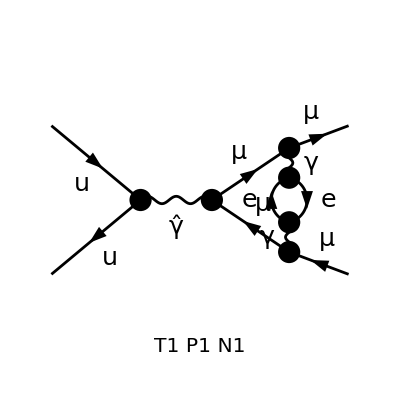

```mathematica
Paint[DiagramExtract[fields2LQEDnoT,7],ColumnsXRows->1];
```

### Tempo di riduzione con kira

```mathematica
tA2=314052.2;
Print["Ore:  ", %/3600]
```

Ore:  87.2367

## B1

```mathematica
userPropagatorMomenta[B1]//MatrixForm
```

(q1
q2
p3+q1
p1+p2+q2
p3+q1+q2
-p1-p2+p3+q1
p1+q2
p1+q1
p3+q2)

```mathematica
userIntegralMasses[B1]
```

{0,M1,M1,M1,0,M1,0,0,0}

Settori Attivi

```mathematica
{1,1,1,1,1,1,0,0,1}
```

> Top. 1 aebe/cfdg/ehfg1f1h212g2h.m, 0 diagrams

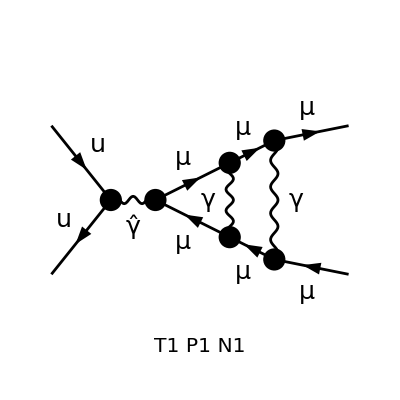

```mathematica
Paint[DiagramExtract[fields2LQEDnoT,2],ColumnsXRows->1];
```

### Tempo di riduzione con kira

```mathematica
tB1=100626.4;
Print["Ore:  ", %/3600]
```

Ore:  27.9518

## B2

```mathematica
userPropagatorMomenta[B2]//MatrixForm
```

(q1
q2
p3+q1
p1+p2+q2
p3+q1+q2
-p1-p2+p3+q1
p1+q2
p1+q1
p3+q2)

```mathematica
userIntegralMasses[B2]
```

{M1,M1,0,M1,M1,0,0,0,0}

Settori Attivi

```mathematica
{1,1,0,1,1,1,0,0,1}
```

> Top. 1 aebe/cfdg/ehfh1f1g212g2h.m, 0 diagrams

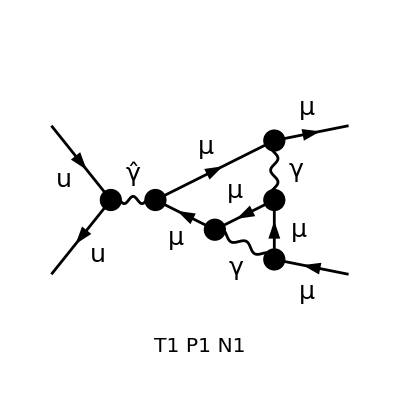

```mathematica
Paint[DiagramExtract[fields2LQEDnoT,3],ColumnsXRows->1];
```

### Tempo di riduzione con kira

```mathematica
tB2= 185494.9;
Print["Ore:  ", %/3600]
```

Ore:  51.5264

## C1

```mathematica
userPropagatorMomenta[C1]//MatrixForm
```

(q1
q2
q1+q2
-p3+q1
-p1-p2+p3+q2
p1+p2-q1-q2
p3+q2
p1-q1
p1-q2)

```mathematica
userIntegralMasses[C1]
```

{M1,0,M1,0,M1,M1,0,0,0}

Settori Attivi

```mathematica
{1,1,1,1,1,1,0,0,0}
```

{1,1,1,1,1,1,0,0,0}

> Top. 1 aebe/cfdg/eh1f1g1h2f2g2h.m, 0 diagrams

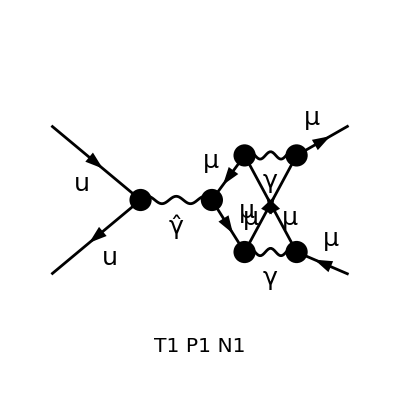

```mathematica
Paint[DiagramExtract[fields2LQEDnoT,4],ColumnsXRows->1];
```

### Tempo di riduzione con kira

```mathematica
tC1= 0;
Print["Ore:  ", %/3600]
```

Ore:  0

In questo caso appunto non sono ancora riuscito a portare a termine la run di kira, per i motivi esposti nella mail